```mathematica
feb01CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\2_01.csv"];
feb15CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\2_15.csv"];
mar01CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\3_01.csv"];
mar15CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\3_15.csv"];
mar29CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\3_29.csv"];
apr12CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\4_12.csv"];
apr26CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\4_26.csv"];
may10CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\5_10.csv"];
may24CrimeData = Import["C:\\Users\\Chris\\workspace\\DVM\\5_24.csv"];
```

```mathematica
feb01Length=Length[Drop[feb01CrimeData,1]];
feb15Length =Length[Drop[feb15CrimeData,1]];
mar01Length=Length[Drop[mar01CrimeData,1]];
mar15Length=Length[Drop[mar15CrimeData,1]];
mar29Length = Length[Drop[mar29CrimeData,1]];
apr12Length=Length[Drop[apr12CrimeData,1]];
apr26Length=Length[Drop[apr26CrimeData,1]];
may10Length=Length[Drop[may10CrimeData,1]];
(*may24Length=Length[Drop[may24CrimeData,1]]*)
keyLength = may10Length;
```

```mathematica
feb01KeyPts=RandomSample[Range[feb01Length],keyLength];
feb15KeyPts = RandomSample[Range[feb15Length],keyLength];
mar01KeyPts=RandomSample[Range[mar01Length],keyLength];
mar15KeyPts = RandomSample[Range[mar15Length],keyLength];
mar29KeyPts = RandomSample[Range[mar29Length],keyLength];
apr12KeyPts = RandomSample[Range[apr12Length], keyLength];
apr26KeyPts = RandomSample[Range[apr26Length],keyLength];
may10KeyPts = RandomSample[Range[may10Length],keyLength] ;
```

```mathematica
feb01KeyValues=Sort[Drop[feb01CrimeData,1]⟦feb01KeyPts⟧];
feb15KeyValues= Sort[Drop[feb15CrimeData,1]⟦feb15KeyPts⟧];
mar01KeyValues = Sort[Drop[mar01CrimeData,1]⟦mar01KeyPts⟧];
mar15KeyValues= Sort[Drop[mar15CrimeData,1]⟦mar15KeyPts⟧];
mar29KeyValues = Sort[Drop[mar29CrimeData,1]⟦mar29KeyPts⟧];
apr12KeyValues = Sort[Drop[apr12CrimeData,1]⟦apr12KeyPts⟧];
apr26KeyValues = Sort[Drop[apr26CrimeData,1]⟦apr26KeyPts⟧];
may10KeyValues = Sort[Drop[may10CrimeData,1]⟦may10KeyPts⟧];
```

```mathematica
feb01Lifelines=Table[feb01KeyValues⟦i,3⟧-feb01KeyValues⟦i,2⟧,{i,keyLength}];
feb15Lifelines=Table[feb15KeyValues⟦i,3⟧-feb15KeyValues⟦i,2⟧,{i,keyLength}];
mar01Lifelines=Table[mar01KeyValues⟦i,3⟧-mar01KeyValues⟦i,2⟧,{i,keyLength}];
mar15Lifelines = Table[mar15KeyValues⟦i,3⟧-mar15KeyValues⟦i,2⟧,{i,keyLength}];
mar29Lifelines = Table[mar29KeyValues⟦i,3⟧-mar29KeyValues⟦i,2⟧,{i,keyLength}];
apr12Lifelines = Table[apr12KeyValues⟦i,3⟧-apr12KeyValues⟦i,2⟧,{i,keyLength}];
apr26Lifelines = Table[apr26KeyValues⟦i,3⟧-apr26KeyValues⟦i,2⟧,{i,keyLength}];
may10Lifelines = Table[may10KeyValues⟦i,3⟧-may10KeyValues⟦i,2⟧,{i,keyLength}];
allLifelines={feb01Lifelines,feb15Lifelines,mar01Lifelines,mar15Lifelines, mar29Lifelines, apr12Lifelines, apr26Lifelines, may10Lifelines};
```

```mathematica
lifelinePerPoint=Table[Table[allLifelines⟦i,k⟧,{i,6}],{k,keyLength}]
```

{{78.,143.,0.,100.,106.,103.},{162.,113.,102.,30.,0.,0.},{4.,20.,0.,89.,109.,0.},{234.,207.,0.,68.,11.,176.},{203.,198.,10.,22.,29.,8.},{2.,2.,191.,4.,190.,189.},{226.,65.,194.,2.,13.,184.},{3.,12.,193.,4.,4.,176.},{72.,83.,86.,4.,229.,32.},{88.,42.,192.,71.,4.,2.},34941,{2.,2.,3.,1.,0.,0.},{2.,3.,2.,0.,0.,0.},{2.,2.,5.,0.,0.,0.},{2.,2.,4.,0.,0.,0.},{2.,4.,2.,1.,0.,0.},{2.,2.,3.,0.,0.,0.},{2.,5.,2.,0.,2.,0.},{1.,5.,2.,0.,2.,0.},{0.,2.,2.,0.,2.,0.},{0.,2.,2.,0.,2.,2.}}
 |  |  |  |

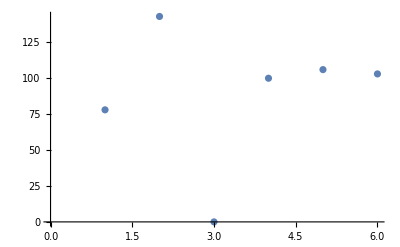

```mathematica
ListPlot[lifelinePerPoint⟦1⟧]
```

```mathematica
AbsoluteTiming[Parallelize[Table[FindFormula[lifelinePerPoint⟦i⟧,x, PerformanceGoal->"Speed", TargetFunctions->{Plus,Times,Power}],{i,10}],Method->"ItemsPerEvaluation" -> 5];]
```

{16.7008,Null}

```mathematica
listOfFunctions=Parallelize[Table[FindFormula[lifelinePerPoint⟦i⟧,x, PerformanceGoal->"Speed", TargetFunctions->{Plus,Times,Power}],{i,Length[lifelinePerPoint]}],Method->"CoarsestGrained"];
```

{Piecewise[{{-45.24+127.4 x-4.16 x^4, 1.≤x<3.8358}, {-14.+46.5 x-4.5 x^2, 3.8358≤x<6.}, {0, True}}],Piecewise[{{161.975+0.0245733 x, 1.≤x<1.93179}, {22.071+45.4645 x, 1.93179≤x<2.5493}, {133.64-3.81918 x-0.0717746 x^5.13288, 2.5493≤x<4.39515}, {0, True}}],-957.+2015.7 x-1460.92 x^2+471.125 x^3-68.5833 x^4+3.675 x^5,-2831.+6516.32 x-4795.63 x^2+1566.83 x^3-235.875 x^4+13.35 x^5,-1716.+3954.83 x-2775.75 x^2+854.25 x^3-120.75 x^4+6.41667 x^5,4693.-10046. x+7493.88 x^2-2499.63 x^3+382.625 x^4-21.8583 x^5,4125.-7966.98 x+5602.46 x^2-1780.33 x^3+260.042 x^4-14.1833 x^5,3486.-7365.57 x+5378. x^2-1736.96 x^3+255.5 x^4-13.975 x^5,2189.-4725.75 x+3738.21 x^2-1334.5 x^3+218.292 x^4-13.25 x^5,-6848.17+1622.69/x^4.0863+11570.4 x-7658.36 x^1.55507+1401.89 x^2.13816-0.441414 x^4.92318,2551.-5010.87 x+3537.42 x^2-1111.58 x^3+159.583 x^4-8.55 x^5,Piecewise[{{113.991+1.00854 x, 1.≤x<1.47531}, {-367.+186. x, 1.47531≤x<3.29583}, {-41.+46.5 x-6.5 x^2, 3.29583≤x<6.}, {0, True}}],-6179.69+1347.92/x^5.30449+11065. x-7543.8 x^1.55507+1426.19 x^2.13816-0.656349 x^4.80478,Piecewise[{{92.-8. x, 1.≤x<2.08197}, {74.1026+13.9658 x, 2.08197≤x<3.38839}, {1667.-660.5 x+65.5 x^2, 3.38839≤x<6.}, {0, True}}],-221.+348.233 x-133.5 x^2+11.5417 x^3+2. x^4-0.275 x^5,1369.-2632.98 x+1857.46 x^2-599. x^3+89.5417 x^4-5.01667 x^5,2479.-4745.68 x+3287.71 x^2-1034.13 x^3+150.292 x^4-8.19167 x^5,240.466-291.804 x+63.515 x^3.-6.15524 x^4.73358+0.0795398 x^7.-0.100792 x^(1. x),716.-1221.97 x+804.167 x^2-243.292 x^3+33.8333 x^4-1.74167 x^5,-1057.+2398.2 x-1773.25 x^2+592.042 x^3-91.25 x^4+5.25833 x^5,-1128.+2373.9 x-1626.58 x^2+498.792 x^3-70.9167 x^4+3.80833 x^5,601.-1008.47 x+595.417 x^2-148. x^3+15.5833 x^4-0.533333 x^5,1367.-2404.22 x+1557.21 x^2-464.792 x^3+65.2917 x^4-3.49167 x^5,565.-1182.18 x+854.125 x^2-272.208 x^3+39.375 x^4-2.10833 x^5,1223.-2796.75 x+2235.46 x^2-773.292 x^3+120.542 x^4-6.95833 x^5,-2029.+4150.25 x-2919.38 x^2+929.208 x^3-136.625 x^4+7.54167 x^5,1754.-3595.2 x+2507.33 x^2-763.333 x^3+105.667 x^4-5.46667 x^5,247.-485.1 x+332.833 x^2-97.2083 x^3+13.1667 x^4-0.691667 x^5,1172.-2450.3 x+1872.33 x^2-625.375 x^3+94.6667 x^4-5.325 x^5,-1338.+2488.75 x-1501.38 x^2+398.583 x^3-48.125 x^4+2.16667 x^5,550.-999.6 x+675.083 x^2-187.542 x^3+21.9167 x^4-0.858333 x^5,-257.+622.6 x-349.333 x^2+68.0833 x^3-3.16667 x^4-0.183333 x^5,-2106.+4466.97 x-3149.17 x^2+993.667 x^3-144.333 x^4+7.86667 x^5,2792.28-5182.41 x+3464.11 x^2.07202-1021.49 x^2.87315+19.6071 x^4.68397-0.0866785 x^7.,3878.-7903.58 x+5659.71 x^2-1815.54 x^3+268.292 x^4-14.875 x^5,-2260.+4670.8 x-3334.67 x^2+1081.04 x^3-162.333 x^4+9.15833 x^5,1027.-2360.75 x+1913.13 x^2-676.917 x^3+107.875 x^4-6.33333 x^5,-2908.+6172.4 x-4408.83 x^2+1418.79 x^3-211.167 x^4+11.8083 x^5,119.-321.75 x+319.625 x^2-137. x^3+25.875 x^4-1.75 x^5,-1661.+3523.85 x-2411.29 x^2+741.458 x^3-105.708 x^4+5.69167 x^5,-1767.+3290.33 x-1994.25 x^2+535.667 x^3-65.75 x^4+3. x^5,1232.-2096.52 x+1319.46 x^2-382.708 x^3+52.5417 x^4-2.775 x^5,-2403.+4821.85 x-3294.13 x^2+1026.42 x^3-149.375 x^4+8.23333 x^5,-72.+194.767 x-150.917 x^2+55.7083 x^3-9.08333 x^4+0.525 x^5,67.+61.85 x+0.458334 x^2-30.0417 x^3+9.54167 x^4-0.808333 x^5,Piecewise[{{62.+47.5 x-22.5 x^2., 1.≤x<3.59173}, {296.-108. x+10. x^2, 3.59173≤x<6.}, {0, True}}],-847.+1546.57 x-837.333 x^2+201.875 x^3-23.1667 x^4+1.05833 x^5,-1054.+2267.45 x-1703.96 x^2+580.208 x^3-91.0417 x^4+5.34167 x^5,733.-1449.97 x+1118.83 x^2-387.875 x^3+61.6667 x^4-3.65833 x^5,632.-1302.88 x+1086.54 x^2-407.333 x^3+68.9583 x^4-4.28333 x^5}

```mathematica
ListPlot[feb01Lifelines,PlotRange->All];
ListPlot[feb15Lifelines,PlotRange->All];
ListPlot[mar01Lifelines,PlotRange->All];
ListPlot[mar15Lifelines,PlotRange->All];
ListPlot[mar29Lifelines,PlotRange->All];
ListPlot[apr12Lifelines,PlotRange->All];
ListPlot[apr26Lifelines,PlotRange->All];
ListPlot[may10Lifelines,PlotRange->All];
```